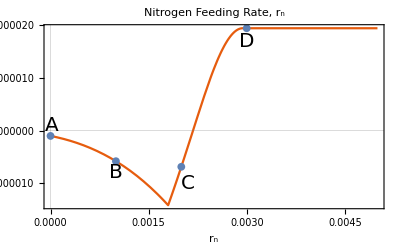
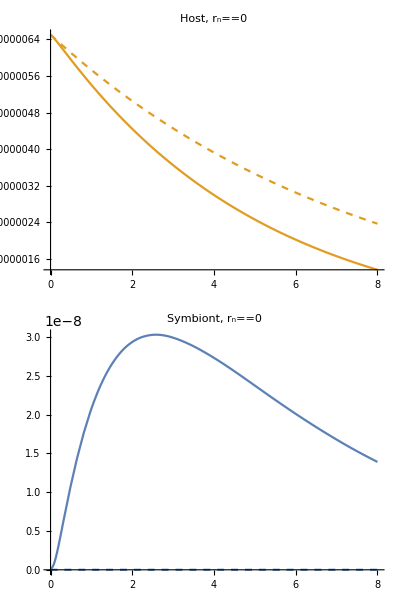
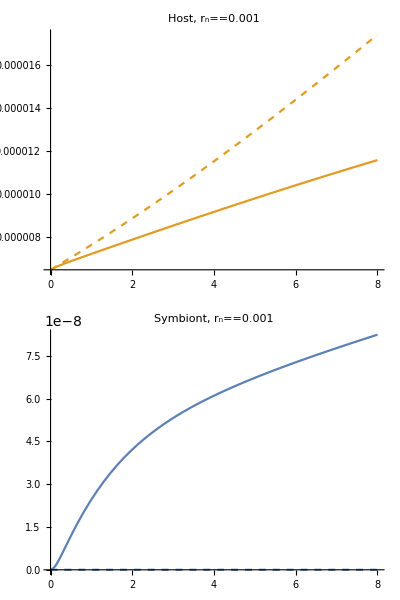
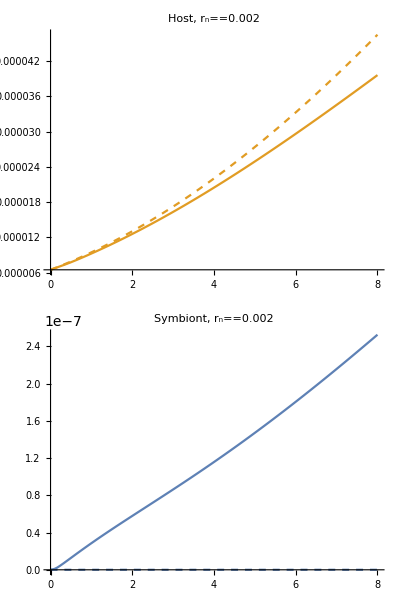
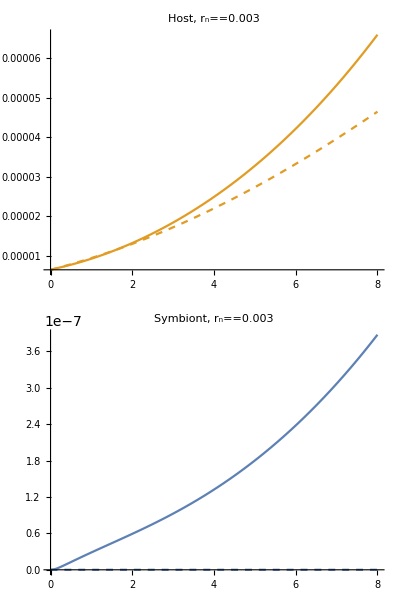
-Graphics-r_nδ
-Graphics-A-Graphics-B-Graphics-C-Graphics-DWeeksC-mol

```mathematica
Clear["Global`*"]
tmax=8; (* 8-week time set *)
colors={h->ColorData[97][2],s->ColorData[97][1]};
parsFixed={nhn->0.18,nsn->0.13}; (*fixed parameters*)
sim[pars_]:=Module[{jsc,jsn,jhc,jhn,jsg,jst,jhg,jht,f},(*Simulation*)
f=s[t](a h[t])/(s[t]+a w h[t]);(*equation 13*)
jsc=p s[t]; (*equation 6*)
jsn=yn nhn f; (*equation 5*)
jhc= p s[t]-Min[jsc,nsn^-1 jsn]+rc h[t]^(2/3);(*equations 10 and 11*)
jhn=rn  h[t]^(2/3);(*equation 9*)
jsg=Min[jsc,nsn^-1 jsn]; (*equation 3*)
jst=ds s[t]; (*equation 4*)
jhg=Min[jhc,nhn^-1 jhn];(*equation 7*)
jht=dh h[t] + f;(*equation 8*)
Quiet@NDSolve[
{
s'[t]==jsg-jst,(*equation 1*)
h'[t]==jhg-jht,(*equation 2*)
s[0]==s0,
h[0]==h0
}/.pars,
{s,h},
{t,0,tmax},Method->{Automatic,"DiscontinuityProcessing"->None},WorkingPrecision->20][[1]]];
pars[treatment_]:=(*parameter choices function*)Piecewise[{{Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->0,h0->h0X},parsFixed], treatment=="as"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->0,h0->h0X},parsFixed], treatment=="af"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->rcX,rn->rnX,s0->s0X,h0->h0X},parsFixed], treatment=="if"}, {Join[{a->aX,w->wX,p->pX,yn->ynX,ds->dsX,dh->dhX,rc->0,rn->0,s0->s0X,h0->h0X},parsFixed], treatment=="is"}}]
bestfit={aX->0.07243165880437435,wX->0.0026142991079086157,pX->27.700459925037663,ynX->0.060192963245436854,dsX->0.7709975010970849,dhX->0.12619563820188512,h0X->6.502940605096842*^-6,s0X->1.0227841615913929*^-10,rcX->0.009992087726261166,rnX->0.014645292219590888};

mutploter[var_,xrange_,yrange_,ynum_,sf_,label_,xlab_]:= (*δ plot function*)Plot[Evaluate[h[8]/.sim[pars["if"]/.var->x/.bestfit]]-Evaluate[h[8]/.sim[pars["af"]/.var->x/.bestfit]],xrange,PlotLabel->Style[label,FontSize->15],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},FrameTicks->{{tk[sf]/@FindDivisions[yrange,ynum],None},{Automatic,None}},
PlotTheme->"Scientific",AxesLabel->{Style[xlab,FontFamily->"Times New Roman",FontColor->Black,FontSize->15],Null},WorkingPrecision->100,ImageSize->400,PlotRange->All]
myticks= Function[{number},{number,ToString[AccountingForm[N[number],{1,sf},NumberSigns->{"-",""},NumberPadding->{" ","0"}]]}];
tk[sfn_]:=myticks/.sf->sfn(*plot tick functions*)
f[x_]:=Evaluate[h[8]/.sim[pars["if"]/.rnX->x/.bestfit]]-Evaluate[h[8]/.sim[pars["af"]/.rnX->x/.bestfit]] (*Calculated δ and point x*)

rnplot=Quiet[mutploter[rnX,{x,0,0.005},{-0.000015,0.00003},7,6,"Nitrogen Feeding Rate,"Subscript["r","n"],Subscript["r","n"]]];(*delta plot for r_n*)
trow=
Show[rnplot,ListPlot[{#,f[#]}&/@{0,0.001,0.002,0.003},PlotMarkers->{Automatic,8}]];(*add points of interest*)
ph[x_]:=Plot[
{
Evaluate[h[t]/.sim[pars["if"]/.rnX->x/.bestfit]],
Evaluate[h[t]/.sim[pars["af"]/.rnX->x/.bestfit]]
},
{t,0,8},PlotStyle->{{h/.colors},{h/.colors,Dashed}},
PlotLabel->"Host, "Subscript[r,n]==ToString[x],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->250,ImagePadding->{{45, 1}, {45, 1}}] (*simulate H at points of interest*)
ps[x_]:=Plot[
{
Evaluate[s[t]/.sim[pars["if"]/.rnX->x/.bestfit]],
Evaluate[s[t]/.sim[pars["af"]/.rnX->x/.bestfit]]
},
{t,0,8},PlotStyle->{{s/.colors},{s/.colors,Dashed}},
PlotLabel->"Symbiont, "Subscript[r,n]==ToString[x],LabelStyle->{FontFamily->"Times New Roman",FontColor->Black},ImageSize->250,ImagePadding->{{45, 1}, {45, 1}}](*simulate S at points of interest*)
tcol[x_]:=Column[{ph[x],ps[x]}] (*column combine simulations*)

col[let_,num_]:=Labeled[tcol[num],Style[let,FontFamily->"Times New Roman",FontSize->20],Top]
brow=Row[{col["A",0],col["B",0.001],col["C",0.002],col["D",0.003]}];
brownew=Labeled[brow,{Style["Weeks", FontFamily->"Times New Roman",FontSize->20],Style["C-mol", FontFamily->"Times New Roman",FontSize->20]},{Bottom,Left},RotateLabel->True];(*label simulations*)
la[let_,spot_]:=Text[
Style[let,FontFamily->"Times New Roman",FontSize->20],spot];(*label points of interest*)
trownew=Labeled[Show[
trow,
Graphics[
{
la["A",{0.00001,0.000001}],
la["B",{0.001,-0.000008}],
la["C",{0.0021,-0.00001}],
la["D",{0.003,0.000017}]}]],
{Style[Subscript["r","n"], FontFamily->"Times New Roman",FontSize->20],Style["δ", FontFamily->"Times New Roman",FontSize->20]},
{Bottom,Left}]; (*full top row plot*)
legend=LineLegend[{h/.colors,{h/.colors,Dashed},{s/.colors},{s/.colors,Dashed}},{"Host With Symbiont","Host Without Symbiont","Symbiont","No Symbiont"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15}]; (*build plot legend*)
trowup=Row[{trownew,legend}];(*top row with legend*)
plot=Column[{trowup,brownew},Center](*complete plot*)
```